```mathematica
ExplainContraction[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
result},
result=Table[
If[EdgeQ[gBis,e[[1]]<->v],
If[EdgeQ[gBis,e[[2]]<->v],
{Style["→→→",Darker[Yellow]],e[[1]]<->v},
{Style["→↑→",Purple],Style[e[[2]]<->v,Darker[Green]]}
],
If[EdgeQ[gBis,e[[2]]<->v],
{Style["↑→→",Blue],Style[e[[1]]<->v,Darker[Green]]},
{Style["↑↑↑",Red],Style[e[[2]]<->v,Red]}
]
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
Join[result,
Map[{Style["↑↑↑",Orange],Style[#,Orange]}&,EdgeList[comp]]
]
]
```

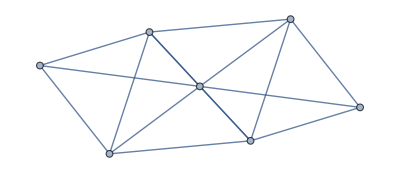

```mathematica
Graph[ReadGrof[5],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]//SortGraph
```

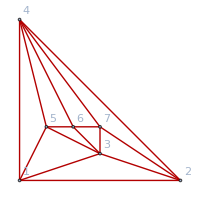
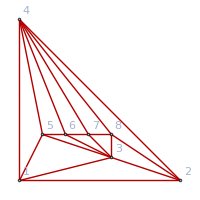
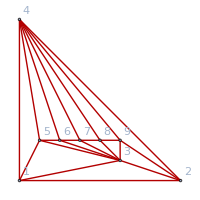
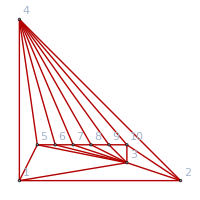
{-Graphics-
{1<->2<->{↑↑↑,2<->6}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑→→,1<->7}
{→↑→,2<->5}
{→→→,1<->3}
{→→→,1<->4},1<->4<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,5<->7}
{↑→→,1<->6}
{↑→→,1<->7}
{→↑→,4<->3}
{→→→,1<->2}
{→→→,1<->5},2<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,5<->7}
{↑→→,2<->5}
{↑→→,2<->6}
{→↑→,4<->3}
{→→→,2<->1}
{→→→,2<->7},3<->1<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,5<->7}
{↑→→,3<->4}
{→↑→,1<->6}
{→↑→,1<->7}
{→→→,3<->2}
{→→→,3<->5},3<->2<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,5<->7}
{↑→→,3<->4}
{→↑→,2<->5}
{→↑→,2<->6}
{→→→,3<->1}
{→→→,3<->7},5<->1<->{↑↑↑,1<->7}
{↑↑↑,2<->6}
{↑↑↑,3<->4}
{↑→→,5<->2}
{→↑→,1<->6}
{→→→,5<->3}
{→→→,5<->4},5<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,2<->6}
{↑→→,5<->2}
{↑→→,5<->7}
{→↑→,3<->4}
{→→→,5<->1}
{→→→,5<->6},5<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,2<->6}
{↑→→,5<->2}
{↑→→,5<->7}
{→↑→,4<->3}
{→→→,5<->1}
{→→→,5<->6},6<->3<->{↑↑↑,1<->7}
{↑↑↑,2<->5}
{↑↑↑,5<->7}
{↑→→,6<->1}
{↑→→,6<->2}
{→↑→,3<->4}
{→→→,6<->5}
{→→→,6<->7},6<->4<->{↑↑↑,1<->7}
{↑↑↑,2<->5}
{↑↑↑,5<->7}
{↑→→,6<->1}
{↑→→,6<->2}
{→↑→,4<->3}
{→→→,6<->5}
{→→→,6<->7},6<->5<->{↑↑↑,5<->2}
{↑↑↑,1<->7}
{↑↑↑,3<->4}
{↑→→,6<->1}
{→↑→,5<->7}
{→→→,6<->3}
{→→→,6<->4},7<->2<->{↑↑↑,2<->5}
{↑↑↑,1<->6}
{↑↑↑,3<->4}
{↑→→,7<->1}
{→↑→,2<->6}
{→→→,7<->3}
{→→→,7<->4},7<->3<->{↑↑↑,1<->6}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑→→,7<->1}
{↑→→,7<->5}
{→↑→,3<->4}
{→→→,7<->2}
{→→→,7<->6},7<->4<->{↑↑↑,1<->6}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑→→,7<->1}
{↑→→,7<->5}
{→↑→,4<->3}
{→→→,7<->2}
{→→→,7<->6},7<->6<->{↑↑↑,6<->1}
{↑↑↑,2<->5}
{↑↑↑,3<->4}
{↑→→,7<->5}
{→↑→,6<->2}
{→→→,7<->3}
{→→→,7<->4}},-Graphics-
{1<->2<->{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,1<->8}
{→↑→,2<->5}
{→→→,1<->3}
{→→→,1<->4},1<->4<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,1<->6}
{↑→→,1<->7}
{↑→→,1<->8}
{→↑→,4<->3}
{→→→,1<->2}
{→→→,1<->5},2<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,2<->5}
{↑→→,2<->6}
{↑→→,2<->7}
{→↑→,4<->3}
{→→→,2<->1}
{→→→,2<->8},3<->1<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,3<->4}
{→↑→,1<->6}
{→↑→,1<->7}
{→↑→,1<->8}
{→→→,3<->2}
{→→→,3<->5},3<->2<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,3<->4}
{→↑→,2<->5}
{→↑→,2<->6}
{→↑→,2<->7}
{→→→,3<->1}
{→→→,3<->8},5<->1<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,3<->4}
{↑↑↑,6<->8}
{↑→→,5<->2}
{→↑→,1<->6}
{→→→,5<->3}
{→→→,5<->4},5<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,6<->8}
{↑→→,5<->2}
{↑→→,5<->7}
{↑→→,5<->8}
{→↑→,3<->4}
{→→→,5<->1}
{→→→,5<->6},5<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,6<->8}
{↑→→,5<->2}
{↑→→,5<->7}
{↑→→,5<->8}
{→↑→,4<->3}
{→→→,5<->1}
{→→→,5<->6},6<->3<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑→→,6<->1}
{↑→→,6<->2}
{↑→→,6<->8}
{→↑→,3<->4}
{→→→,6<->5}
{→→→,6<->7},6<->4<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑→→,6<->1}
{↑→→,6<->2}
{↑→→,6<->8}
{→↑→,4<->3}
{→→→,6<->5}
{→→→,6<->7},6<->5<->{↑↑↑,5<->2}
{↑↑↑,5<->8}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->7}
{↑↑↑,3<->4}
{↑→→,6<->1}
{→↑→,5<->7}
{→→→,6<->3}
{→→→,6<->4},7<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,7<->1}
{↑→→,7<->2}
{↑→→,7<->5}
{→↑→,3<->4}
{→→→,7<->6}
{→→→,7<->8},7<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,7<->1}
{↑→→,7<->2}
{↑→→,7<->5}
{→↑→,4<->3}
{→→→,7<->6}
{→→→,7<->8},7<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->2}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,3<->4}
{↑↑↑,5<->8}
{↑→→,7<->5}
{→↑→,6<->8}
{→→→,7<->3}
{→→→,7<->4},8<->2<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑→→,8<->1}
{→↑→,2<->7}
{→→→,8<->3}
{→→→,8<->4},8<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑→→,8<->1}
{↑→→,8<->5}
{↑→→,8<->6}
{→↑→,3<->4}
{→→→,8<->2}
{→→→,8<->7},8<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑→→,8<->1}
{↑→→,8<->5}
{↑→→,8<->6}
{→↑→,4<->3}
{→→→,8<->2}
{→→→,8<->7},8<->7<->{↑↑↑,7<->1}
{↑↑↑,7<->5}
{↑↑↑,1<->6}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,3<->4}
{↑→→,8<->6}
{→↑→,7<->2}
{→→→,8<->3}
{→→→,8<->4}},-Graphics-
{1<->2<->{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,1<->9}
{→↑→,2<->5}
{→→→,1<->3}
{→→→,1<->4},1<->4<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,1<->6}
{↑→→,1<->7}
{↑→→,1<->8}
{↑→→,1<->9}
{→↑→,4<->3}
{→→→,1<->2}
{→→→,1<->5},2<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,2<->5}
{↑→→,2<->6}
{↑→→,2<->7}
{↑→→,2<->8}
{→↑→,4<->3}
{→→→,2<->1}
{→→→,2<->9},3<->1<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,3<->4}
{→↑→,1<->6}
{→↑→,1<->7}
{→↑→,1<->8}
{→↑→,1<->9}
{→→→,3<->2}
{→→→,3<->5},3<->2<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,3<->4}
{→↑→,2<->5}
{→↑→,2<->6}
{→↑→,2<->7}
{→↑→,2<->8}
{→→→,3<->1}
{→→→,3<->9},5<->1<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,5<->2}
{→↑→,1<->6}
{→→→,5<->3}
{→→→,5<->4},5<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,5<->2}
{↑→→,5<->7}
{↑→→,5<->8}
{↑→→,5<->9}
{→↑→,3<->4}
{→→→,5<->1}
{→→→,5<->6},5<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,5<->2}
{↑→→,5<->7}
{↑→→,5<->8}
{↑→→,5<->9}
{→↑→,4<->3}
{→→→,5<->1}
{→→→,5<->6},6<->3<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,7<->9}
{↑→→,6<->1}
{↑→→,6<->2}
{↑→→,6<->8}
{↑→→,6<->9}
{→↑→,3<->4}
{→→→,6<->5}
{→→→,6<->7},6<->4<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,7<->9}
{↑→→,6<->1}
{↑→→,6<->2}
{↑→→,6<->8}
{↑→→,6<->9}
{→↑→,4<->3}
{→→→,6<->5}
{→→→,6<->7},6<->5<->{↑↑↑,5<->2}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,7<->9}
{↑→→,6<->1}
{→↑→,5<->7}
{→→→,6<->3}
{→→→,6<->4},7<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑→→,7<->1}
{↑→→,7<->2}
{↑→→,7<->5}
{↑→→,7<->9}
{→↑→,3<->4}
{→→→,7<->6}
{→→→,7<->8},7<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑→→,7<->1}
{↑→→,7<->2}
{↑→→,7<->5}
{↑→→,7<->9}
{→↑→,4<->3}
{→→→,7<->6}
{→→→,7<->8},7<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->2}
{↑↑↑,6<->9}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑→→,7<->5}
{→↑→,6<->8}
{→→→,7<->3}
{→→→,7<->4},8<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑↑↑,5<->9}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,8<->1}
{↑→→,8<->2}
{↑→→,8<->5}
{↑→→,8<->6}
{→↑→,3<->4}
{→→→,8<->7}
{→→→,8<->9},8<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,5<->7}
{↑↑↑,5<->9}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,8<->1}
{↑→→,8<->2}
{↑→→,8<->5}
{↑→→,8<->6}
{→↑→,4<->3}
{→→→,8<->7}
{→→→,8<->9},8<->7<->{↑↑↑,7<->1}
{↑↑↑,7<->2}
{↑↑↑,7<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,3<->4}
{↑↑↑,5<->9}
{↑↑↑,6<->9}
{↑→→,8<->6}
{→↑→,7<->9}
{→→→,8<->3}
{→→→,8<->4},9<->2<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,9<->1}
{→↑→,2<->8}
{→→→,9<->3}
{→→→,9<->4},9<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,9<->1}
{↑→→,9<->5}
{↑→→,9<->6}
{↑→→,9<->7}
{→↑→,3<->4}
{→→→,9<->2}
{→→→,9<->8},9<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,9<->1}
{↑→→,9<->5}
{↑→→,9<->6}
{↑→→,9<->7}
{→↑→,4<->3}
{→→→,9<->2}
{→→→,9<->8},9<->8<->{↑↑↑,8<->1}
{↑↑↑,8<->5}
{↑↑↑,8<->6}
{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑→→,9<->7}
{→↑→,8<->2}
{→→→,9<->3}
{→→→,9<->4}},-Graphics-
{1<->2<->{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,1<->10}
{→↑→,2<->5}
{→→→,1<->3}
{→→→,1<->4},1<->4<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,1<->6}
{↑→→,1<->7}
{↑→→,1<->8}
{↑→→,1<->9}
{↑→→,1<->10}
{→↑→,4<->3}
{→→→,1<->2}
{→→→,1<->5},2<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,2<->5}
{↑→→,2<->6}
{↑→→,2<->7}
{↑→→,2<->8}
{↑→→,2<->9}
{→↑→,4<->3}
{→→→,2<->1}
{→→→,2<->10},3<->1<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,3<->4}
{→↑→,1<->6}
{→↑→,1<->7}
{→↑→,1<->8}
{→↑→,1<->9}
{→↑→,1<->10}
{→→→,3<->2}
{→→→,3<->5},3<->2<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,3<->4}
{→↑→,2<->5}
{→↑→,2<->6}
{→↑→,2<->7}
{→↑→,2<->8}
{→↑→,2<->9}
{→→→,3<->1}
{→→→,3<->10},5<->1<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,3<->4}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,5<->2}
{→↑→,1<->6}
{→→→,5<->3}
{→→→,5<->4},5<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,5<->2}
{↑→→,5<->7}
{↑→→,5<->8}
{↑→→,5<->9}
{↑→→,5<->10}
{→↑→,3<->4}
{→→→,5<->1}
{→→→,5<->6},5<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,5<->2}
{↑→→,5<->7}
{↑→→,5<->8}
{↑→→,5<->9}
{↑→→,5<->10}
{→↑→,4<->3}
{→→→,5<->1}
{→→→,5<->6},6<->3<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,6<->1}
{↑→→,6<->2}
{↑→→,6<->8}
{↑→→,6<->9}
{↑→→,6<->10}
{→↑→,3<->4}
{→→→,6<->5}
{→→→,6<->7},6<->4<->{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,6<->1}
{↑→→,6<->2}
{↑→→,6<->8}
{↑→→,6<->9}
{↑→→,6<->10}
{→↑→,4<->3}
{→→→,6<->5}
{→→→,6<->7},6<->5<->{↑↑↑,5<->2}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,3<->4}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,6<->1}
{→↑→,5<->7}
{→→→,6<->3}
{→→→,6<->4},7<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,8<->10}
{↑→→,7<->1}
{↑→→,7<->2}
{↑→→,7<->5}
{↑→→,7<->9}
{↑→→,7<->10}
{→↑→,3<->4}
{→→→,7<->6}
{→→→,7<->8},7<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,8<->10}
{↑→→,7<->1}
{↑→→,7<->2}
{↑→→,7<->5}
{↑→→,7<->9}
{↑→→,7<->10}
{→↑→,4<->3}
{→→→,7<->6}
{→→→,7<->8},7<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->2}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,3<->4}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,8<->10}
{↑→→,7<->5}
{→↑→,6<->8}
{→→→,7<->3}
{→→→,7<->4},8<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑→→,8<->1}
{↑→→,8<->2}
{↑→→,8<->5}
{↑→→,8<->6}
{↑→→,8<->10}
{→↑→,3<->4}
{→→→,8<->7}
{→→→,8<->9},8<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑→→,8<->1}
{↑→→,8<->2}
{↑→→,8<->5}
{↑→→,8<->6}
{↑→→,8<->10}
{→↑→,4<->3}
{→→→,8<->7}
{→→→,8<->9},8<->7<->{↑↑↑,7<->1}
{↑↑↑,7<->2}
{↑↑↑,7<->5}
{↑↑↑,7<->10}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->9}
{↑↑↑,3<->4}
{↑↑↑,5<->9}
{↑↑↑,5<->10}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑→→,8<->6}
{→↑→,7<->9}
{→→→,8<->3}
{→→→,8<->4},9<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->10}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,9<->1}
{↑→→,9<->2}
{↑→→,9<->5}
{↑→→,9<->6}
{↑→→,9<->7}
{→↑→,3<->4}
{→→→,9<->8}
{→→→,9<->10},9<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->10}
{↑↑↑,6<->8}
{↑↑↑,6<->10}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,9<->1}
{↑→→,9<->2}
{↑→→,9<->5}
{↑→→,9<->6}
{↑→→,9<->7}
{→↑→,4<->3}
{→→→,9<->8}
{→→→,9<->10},9<->8<->{↑↑↑,8<->1}
{↑↑↑,8<->2}
{↑↑↑,8<->5}
{↑↑↑,8<->6}
{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->10}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑↑↑,5<->10}
{↑↑↑,6<->10}
{↑↑↑,7<->10}
{↑→→,9<->7}
{→↑→,8<->10}
{→→→,9<->3}
{→→→,9<->4},10<->2<->{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,10<->1}
{→↑→,2<->9}
{→→→,10<->3}
{→→→,10<->4},10<->3<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,10<->1}
{↑→→,10<->5}
{↑→→,10<->6}
{↑→→,10<->7}
{↑→→,10<->8}
{→↑→,3<->4}
{→→→,10<->2}
{→→→,10<->9},10<->4<->{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,2<->9}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑→→,10<->1}
{↑→→,10<->5}
{↑→→,10<->6}
{↑→→,10<->7}
{↑→→,10<->8}
{→↑→,4<->3}
{→→→,10<->2}
{→→→,10<->9},10<->9<->{↑↑↑,9<->1}
{↑↑↑,9<->5}
{↑↑↑,9<->6}
{↑↑↑,9<->7}
{↑↑↑,1<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,2<->5}
{↑↑↑,2<->6}
{↑↑↑,2<->7}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑→→,10<->8}
{→↑→,9<->2}
{→→→,10<->3}
{→→→,10<->4}}}

```mathematica
Table[
With[{g=JacobsThalGraph[k]},
Column[{Graph[g,VertexLabels->"Name", GraphLayout->"PlanarEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],
Sort[Table[
e<->Column[Sort[ExplainContraction[g,e]]],{e,CollectMPGEdges[g]}
]]}]]
,{k,3,6}]
```

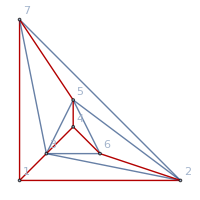
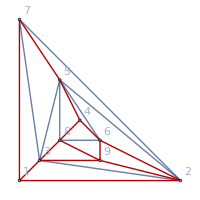
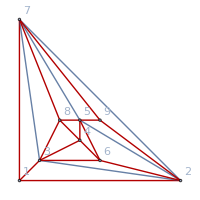
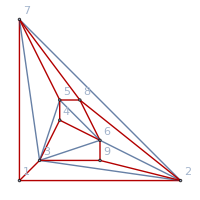
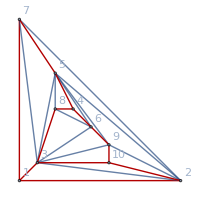
{-Graphics-
{1<->2<->{↑↑↑,2<->4}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑→→,1<->5}
{↑→→,1<->6}
{→→→,1<->3}
{→→→,1<->7},1<->3<->{↑↑↑,2<->4}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑→→,1<->4}
{↑→→,1<->5}
{↑→→,1<->6}
{→→→,1<->2}
{→→→,1<->7},1<->7<->{↑↑↑,7<->4}
{↑↑↑,7<->6}
{↑↑↑,2<->4}
{↑→→,1<->5}
{→→→,1<->2}
{→→→,1<->3},2<->6<->{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,4<->7}
{↑→→,2<->4}
{→↑→,6<->1}
{→↑→,6<->7}
{→→→,2<->3}
{→→→,2<->5},3<->4<->{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,6<->7}
{→↑→,4<->1}
{→↑→,4<->2}
{→↑→,4<->7}
{→→→,3<->5}
{→→→,3<->6},4<->5<->{↑↑↑,5<->1}
{↑↑↑,1<->6}
{↑↑↑,6<->7}
{↑→→,4<->2}
{↑→→,4<->7}
{→→→,4<->3}
{→→→,4<->6},4<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->7}
{↑↑↑,1<->5}
{↑→→,4<->2}
{→→→,4<->3}
{→→→,4<->5},5<->7<->{↑↑↑,1<->4}
{↑↑↑,1<->6}
{↑↑↑,2<->4}
{↑→→,5<->1}
{→↑→,7<->4}
{→↑→,7<->6}
{→→→,5<->2}
{→→→,5<->3}},-Graphics-
{1<->2<->{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,3<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑→→,1<->5}
{↑→→,1<->6}
{↑→→,1<->9}
{→→→,1<->3}
{→→→,1<->7},1<->3<->{↑↑↑,3<->4}
{↑↑↑,3<->6}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑→→,1<->5}
{↑→→,1<->8}
{↑→→,1<->9}
{→→→,1<->2}
{→→→,1<->7},1<->7<->{↑↑↑,7<->4}
{↑↑↑,7<->6}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,3<->6}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑→→,1<->5}
{→→→,1<->2}
{→→→,1<->3},2<->6<->{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,3<->4}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑→→,2<->4}
{↑→→,2<->8}
{→↑→,6<->1}
{→↑→,6<->3}
{→↑→,6<->7}
{→→→,2<->5}
{→→→,2<->9},2<->9<->{↑↑↑,9<->4}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,3<->4}
{↑↑↑,3<->6}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{↑→→,2<->8}
{→↑→,9<->1}
{→↑→,9<->5}
{→↑→,9<->7}
{→→→,2<->3}
{→→→,2<->6},3<->8<->{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑→→,3<->4}
{↑→→,3<->6}
{→↑→,8<->1}
{→↑→,8<->2}
{→↑→,8<->7}
{→→→,3<->5}
{→→→,3<->9},3<->9<->{↑↑↑,9<->4}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{↑→→,3<->6}
{→↑→,9<->1}
{→↑→,9<->5}
{→↑→,9<->7}
{→→→,3<->2}
{→→→,3<->8},4<->5<->{↑↑↑,5<->1}
{↑↑↑,5<->9}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->8}
{↑↑↑,3<->6}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑→→,4<->2}
{↑→→,4<->3}
{↑→→,4<->7}
{→→→,4<->6}
{→→→,4<->8},4<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->3}
{↑↑↑,6<->7}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->8}
{↑↑↑,5<->9}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑→→,4<->2}
{↑→→,4<->9}
{→→→,4<->5}
{→→→,4<->8},4<->8<->{↑↑↑,8<->1}
{↑↑↑,8<->2}
{↑↑↑,8<->7}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,3<->6}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑→→,4<->3}
{↑→→,4<->9}
{→→→,4<->5}
{→→→,4<->6},5<->7<->{↑↑↑,7<->9}
{↑↑↑,1<->4}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,3<->6}
{↑↑↑,4<->9}
{↑→→,5<->1}
{→↑→,7<->4}
{→↑→,7<->6}
{→↑→,7<->8}
{→→→,5<->2}
{→→→,5<->3},6<->9<->{↑↑↑,9<->1}
{↑↑↑,9<->7}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,4<->7}
{↑↑↑,7<->8}
{↑→→,6<->3}
{→↑→,9<->4}
{→↑→,9<->5}
{→→→,6<->2}
{→→→,6<->8},8<->9<->{↑↑↑,9<->1}
{↑↑↑,9<->7}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,2<->4}
{↑↑↑,3<->4}
{↑↑↑,3<->6}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑→→,8<->2}
{→↑→,9<->4}
{→↑→,9<->5}
{→→→,8<->3}
{→→→,8<->6}},-Graphics-
{1<->2<->{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->5}
{↑↑↑,3<->9}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,6<->7}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,8<->9}
{↑→→,1<->5}
{↑→→,1<->6}
{↑→→,1<->9}
{→→→,1<->3}
{→→→,1<->7},1<->3<->{↑↑↑,3<->5}
{↑↑↑,3<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,6<->7}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,8<->9}
{↑→→,1<->4}
{↑→→,1<->6}
{↑→→,1<->8}
{→→→,1<->2}
{→→→,1<->7},1<->7<->{↑↑↑,7<->4}
{↑↑↑,7<->6}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->5}
{↑↑↑,3<->9}
{↑↑↑,4<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,8<->9}
{↑→→,1<->5}
{↑→→,1<->8}
{↑→→,1<->9}
{→→→,1<->2}
{→→→,1<->3},2<->6<->{↑↑↑,6<->8}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,3<->5}
{↑↑↑,3<->9}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,8<->9}
{↑→→,2<->4}
{→↑→,6<->1}
{→↑→,6<->7}
{→↑→,6<->9}
{→→→,2<->3}
{→→→,2<->5},2<->9<->{↑↑↑,9<->4}
{↑↑↑,9<->8}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,3<->5}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑↑↑,6<->8}
{→↑→,9<->1}
{→↑→,9<->3}
{→↑→,9<->6}
{→→→,2<->5}
{→→→,2<->7},3<->4<->{↑↑↑,4<->9}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->8}
{↑↑↑,6<->7}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,8<->9}
{↑→→,3<->5}
{→↑→,4<->1}
{→↑→,4<->2}
{→↑→,4<->7}
{→→→,3<->6}
{→→→,3<->8},3<->6<->{↑↑↑,6<->9}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,8<->9}
{↑→→,3<->5}
{→↑→,6<->1}
{→↑→,6<->7}
{→↑→,6<->8}
{→→→,3<->2}
{→→→,3<->4},3<->8<->{↑↑↑,8<->9}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,6<->7}
{↑↑↑,6<->9}
{↑→→,3<->5}
{→↑→,8<->1}
{→↑→,8<->2}
{→↑→,8<->6}
{→→→,3<->4}
{→→→,3<->7},4<->5<->{↑↑↑,5<->1}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->8}
{↑↑↑,3<->9}
{↑↑↑,6<->7}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,8<->9}
{↑→→,4<->2}
{↑→→,4<->7}
{↑→→,4<->9}
{→↑→,5<->3}
{→→→,4<->6}
{→→→,4<->8},4<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->7}
{↑↑↑,6<->9}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->8}
{↑↑↑,3<->5}
{↑↑↑,3<->9}
{↑↑↑,8<->9}
{↑→→,4<->2}
{→↑→,6<->8}
{→→→,4<->3}
{→→→,4<->5},4<->8<->{↑↑↑,8<->1}
{↑↑↑,8<->2}
{↑↑↑,8<->9}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,3<->5}
{↑↑↑,3<->9}
{↑↑↑,6<->7}
{↑↑↑,6<->9}
{↑→→,4<->7}
{→↑→,8<->6}
{→→→,4<->3}
{→→→,4<->5},5<->6<->{↑↑↑,6<->1}
{↑↑↑,1<->4}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->9}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,8<->9}
{↑→→,5<->3}
{→↑→,6<->7}
{→↑→,6<->8}
{→↑→,6<->9}
{→→→,5<->2}
{→→→,5<->4},5<->8<->{↑↑↑,8<->1}
{↑↑↑,1<->4}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,3<->9}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,6<->7}
{↑↑↑,6<->9}
{↑→→,5<->3}
{→↑→,8<->2}
{→↑→,8<->6}
{→↑→,8<->9}
{→→→,5<->4}
{→→→,5<->7},5<->9<->{↑↑↑,9<->1}
{↑↑↑,9<->3}
{↑↑↑,1<->4}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑↑↑,6<->8}
{→↑→,9<->4}
{→↑→,9<->6}
{→↑→,9<->8}
{→→→,5<->2}
{→→→,5<->7},7<->8<->{↑↑↑,8<->6}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,3<->5}
{↑↑↑,3<->9}
{↑↑↑,4<->9}
{↑↑↑,6<->9}
{↑→→,7<->4}
{→↑→,8<->1}
{→↑→,8<->2}
{→↑→,8<->9}
{→→→,7<->3}
{→→→,7<->5},7<->9<->{↑↑↑,9<->4}
{↑↑↑,9<->6}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->5}
{↑↑↑,6<->8}
{→↑→,9<->1}
{→↑→,9<->3}
{→↑→,9<->8}
{→→→,7<->2}
{→→→,7<->5}},-Graphics-
{1<->2<->{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,3<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑↑↑,8<->9}
{↑→→,1<->6}
{↑→→,1<->8}
{↑→→,1<->9}
{→→→,1<->3}
{→→→,1<->7},1<->3<->{↑↑↑,3<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑↑↑,8<->9}
{↑→→,1<->4}
{↑→→,1<->5}
{↑→→,1<->6}
{↑→→,1<->9}
{→→→,1<->2}
{→→→,1<->7},1<->7<->{↑↑↑,7<->4}
{↑↑↑,7<->6}
{↑↑↑,7<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,3<->8}
{↑↑↑,4<->8}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,8<->9}
{↑→→,1<->5}
{↑→→,1<->8}
{→→→,1<->2}
{→→→,1<->3},2<->8<->{↑↑↑,8<->4}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑→→,2<->5}
{→↑→,8<->1}
{→↑→,8<->3}
{→↑→,8<->9}
{→→→,2<->6}
{→→→,2<->7},2<->9<->{↑↑↑,9<->4}
{↑↑↑,9<->5}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,3<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,6<->7}
{→↑→,9<->1}
{→↑→,9<->7}
{→↑→,9<->8}
{→→→,2<->3}
{→→→,2<->6},3<->4<->{↑↑↑,4<->8}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,5<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑↑↑,8<->9}
{→↑→,4<->1}
{→↑→,4<->2}
{→↑→,4<->7}
{→↑→,4<->9}
{→→→,3<->5}
{→→→,3<->6},3<->9<->{↑↑↑,9<->8}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,6<->7}
{→↑→,9<->1}
{→↑→,9<->4}
{→↑→,9<->5}
{→↑→,9<->7}
{→→→,3<->2}
{→→→,3<->6},4<->5<->{↑↑↑,5<->1}
{↑↑↑,5<->2}
{↑↑↑,5<->9}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,3<->8}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑↑↑,8<->9}
{↑→→,4<->7}
{↑→→,4<->8}
{→→→,4<->3}
{→→→,4<->6},4<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->7}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->5}
{↑↑↑,3<->8}
{↑↑↑,5<->9}
{↑↑↑,7<->9}
{↑↑↑,8<->9}
{↑→→,4<->2}
{↑→→,4<->8}
{↑→→,4<->9}
{→→→,4<->3}
{→→→,4<->5},5<->7<->{↑↑↑,7<->9}
{↑↑↑,1<->4}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,3<->8}
{↑↑↑,4<->8}
{↑↑↑,4<->9}
{↑↑↑,8<->9}
{↑→→,5<->1}
{↑→→,5<->2}
{→↑→,7<->4}
{→↑→,7<->6}
{→→→,5<->3}
{→→→,5<->8},5<->8<->{↑↑↑,8<->1}
{↑↑↑,8<->9}
{↑↑↑,1<->4}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->9}
{↑→→,5<->2}
{→↑→,8<->3}
{→↑→,8<->4}
{→→→,5<->6}
{→→→,5<->7},6<->8<->{↑↑↑,8<->1}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑↑↑,7<->9}
{↑→→,6<->7}
{→↑→,8<->3}
{→↑→,8<->4}
{→↑→,8<->9}
{→→→,6<->2}
{→→→,6<->5},6<->9<->{↑↑↑,9<->1}
{↑↑↑,9<->7}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,3<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{→↑→,9<->4}
{→↑→,9<->5}
{→↑→,9<->8}
{→→→,6<->2}
{→→→,6<->3},7<->8<->{↑↑↑,8<->4}
{↑↑↑,8<->9}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,4<->9}
{↑↑↑,5<->9}
{↑→→,7<->6}
{→↑→,8<->1}
{→↑→,8<->3}
{→→→,7<->2}
{→→→,7<->5}},-Graphics-
{1<->2<->{↑↑↑,2<->4}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,4<->10}
{↑↑↑,5<->10}
{↑↑↑,6<->7}
{↑↑↑,6<->10}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->9}
{↑↑↑,8<->10}
{↑→→,1<->5}
{↑→→,1<->9}
{↑→→,1<->10}
{→→→,1<->3}
{→→→,1<->7},1<->3<->{↑↑↑,3<->4}
{↑↑↑,2<->4}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,4<->10}
{↑↑↑,5<->10}
{↑↑↑,6<->7}
{↑↑↑,6<->10}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->9}
{↑↑↑,8<->10}
{↑→→,1<->5}
{↑→→,1<->6}
{↑→→,1<->8}
{↑→→,1<->9}
{↑→→,1<->10}
{→→→,1<->2}
{→→→,1<->7},1<->7<->{↑↑↑,7<->4}
{↑↑↑,7<->6}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,2<->4}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,4<->9}
{↑↑↑,4<->10}
{↑↑↑,5<->10}
{↑↑↑,6<->10}
{↑↑↑,8<->9}
{↑↑↑,8<->10}
{↑→→,1<->5}
{→→→,1<->2}
{→→→,1<->3},2<->10<->{↑↑↑,10<->4}
{↑↑↑,10<->6}
{↑↑↑,10<->8}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,3<->4}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,8<->9}
{→↑→,10<->1}
{→↑→,10<->5}
{→↑→,10<->7}
{→→→,2<->3}
{→→→,2<->9},3<->8<->{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->4}
{↑↑↑,2<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,4<->10}
{↑↑↑,5<->10}
{↑↑↑,6<->7}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑→→,3<->4}
{→↑→,8<->1}
{→↑→,8<->2}
{→↑→,8<->7}
{→↑→,8<->9}
{→↑→,8<->10}
{→→→,3<->5}
{→→→,3<->6},3<->10<->{↑↑↑,10<->4}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,2<->4}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,4<->7}
{↑↑↑,4<->9}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,8<->9}
{→↑→,10<->1}
{→↑→,10<->5}
{→↑→,10<->6}
{→↑→,10<->7}
{→↑→,10<->8}
{→→→,3<->2}
{→→→,3<->9},4<->5<->{↑↑↑,5<->1}
{↑↑↑,5<->10}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,6<->7}
{↑↑↑,6<->10}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->9}
{↑↑↑,8<->10}
{↑→→,4<->2}
{↑→→,4<->3}
{↑→→,4<->7}
{↑→→,4<->9}
{→→→,4<->6}
{→→→,4<->8},4<->6<->{↑↑↑,6<->1}
{↑↑↑,6<->2}
{↑↑↑,6<->7}
{↑↑↑,6<->10}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->8}
{↑↑↑,5<->10}
{↑↑↑,7<->8}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->9}
{↑↑↑,8<->10}
{↑→→,4<->3}
{↑→→,4<->9}
{→→→,4<->5}
{→→→,4<->8},4<->8<->{↑↑↑,8<->1}
{↑↑↑,8<->2}
{↑↑↑,8<->7}
{↑↑↑,8<->9}
{↑↑↑,8<->10}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->6}
{↑↑↑,5<->10}
{↑↑↑,6<->7}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑→→,4<->3}
{→→→,4<->5}
{→→→,4<->6},5<->7<->{↑↑↑,7<->10}
{↑↑↑,1<->4}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->4}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,4<->9}
{↑↑↑,4<->10}
{↑↑↑,6<->10}
{↑↑↑,8<->9}
{↑↑↑,8<->10}
{↑→→,5<->1}
{→↑→,7<->4}
{→↑→,7<->6}
{→↑→,7<->8}
{→↑→,7<->9}
{→→→,5<->2}
{→→→,5<->3},6<->9<->{↑↑↑,9<->1}
{↑↑↑,9<->7}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->10}
{↑↑↑,2<->4}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,4<->7}
{↑↑↑,4<->10}
{↑↑↑,5<->10}
{↑↑↑,7<->8}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,6<->2}
{↑→→,6<->10}
{→↑→,9<->4}
{→↑→,9<->8}
{→→→,6<->3}
{→→→,6<->5},9<->10<->{↑↑↑,10<->1}
{↑↑↑,10<->4}
{↑↑↑,10<->7}
{↑↑↑,10<->8}
{↑↑↑,1<->4}
{↑↑↑,1<->5}
{↑↑↑,1<->6}
{↑↑↑,1<->8}
{↑↑↑,2<->4}
{↑↑↑,2<->6}
{↑↑↑,2<->8}
{↑↑↑,3<->4}
{↑↑↑,4<->7}
{↑↑↑,6<->7}
{↑↑↑,7<->8}
{→↑→,10<->5}
{→↑→,10<->6}
{→→→,9<->2}
{→→→,9<->3}}}

```mathematica
Table[
With[{g=ReadGrof[k]},
Column[{Graph[g,VertexLabels->"Name", GraphLayout->"PlanarEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],
Sort[Table[
e<->Column[Sort[ExplainContraction[g,e]]],{e,CollectMPGEdges[g]}
]]}]]
,{k,5,100,20}]
```

```mathematica
Graph[plantri [[1]] ]
```

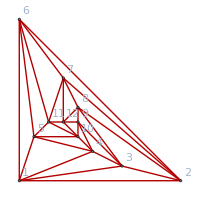
-Graphics-
{1<->2<->{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,1<->7}
{↑→→,1<->8}
{→↑→,2<->4}
{→↑→,2<->5}
{→→→,1<->3}
{→→→,1<->6},1<->3<->{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,1<->8}
{↑→→,1<->9}
{→↑→,3<->5}
{→↑→,3<->6}
{→→→,1<->2}
{→→→,1<->4},1<->4<->{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,1<->9}
{↑→→,1<->10}
{→↑→,4<->2}
{→↑→,4<->6}
{→→→,1<->3}
{→→→,1<->5},1<->5<->{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,1<->10}
{↑→→,1<->11}
{→↑→,5<->2}
{→↑→,5<->3}
{→→→,1<->4}
{→→→,1<->6},1<->6<->{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,1<->7}
{↑→→,1<->11}
{→↑→,6<->3}
{→↑→,6<->4}
{→→→,1<->2}
{→→→,1<->5},2<->3<->{↑↑↑,3<->5}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,2<->4}
{↑→→,2<->9}
{→↑→,3<->6}
{→↑→,3<->7}
{→→→,2<->1}
{→→→,2<->8},2<->6<->{↑↑↑,6<->4}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,2<->5}
{↑→→,2<->11}
{→↑→,6<->3}
{→↑→,6<->8}
{→→→,2<->1}
{→→→,2<->7},2<->7<->{↑↑↑,7<->4}
{↑↑↑,7<->5}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,2<->11}
{↑→→,2<->12}
{→↑→,7<->1}
{→↑→,7<->3}
{→→→,2<->6}
{→→→,2<->8},2<->8<->{↑↑↑,8<->4}
{↑↑↑,8<->5}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,1<->7}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,9<->11}
{↑→→,2<->9}
{↑→→,2<->12}
{→↑→,8<->1}
{→↑→,8<->6}
{→→→,2<->3}
{→→→,2<->7},3<->4<->{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,3<->5}
{↑→→,3<->10}
{→↑→,4<->2}
{→↑→,4<->8}
{→→→,3<->1}
{→→→,3<->9},3<->8<->{↑↑↑,8<->5}
{↑↑↑,8<->6}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,1<->7}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,9<->11}
{↑→→,3<->7}
{↑→→,3<->12}
{→↑→,8<->1}
{→↑→,8<->4}
{→→→,3<->2}
{→→→,3<->9},3<->9<->{↑↑↑,9<->5}
{↑↑↑,9<->6}
{↑↑↑,9<->7}
{↑↑↑,9<->11}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑→→,3<->10}
{↑→→,3<->12}
{→↑→,9<->1}
{→↑→,9<->2}
{→→→,3<->4}
{→→→,3<->8},4<->5<->{↑↑↑,5<->2}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->12}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,4<->6}
{↑→→,4<->11}
{→↑→,5<->3}
{→↑→,5<->9}
{→→→,4<->1}
{→→→,4<->10},4<->9<->{↑↑↑,9<->2}
{↑↑↑,9<->6}
{↑↑↑,9<->7}
{↑↑↑,9<->11}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->5}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑→→,4<->8}
{↑→→,4<->12}
{→↑→,9<->1}
{→↑→,9<->5}
{→→→,4<->3}
{→→→,4<->10},4<->10<->{↑↑↑,10<->2}
{↑↑↑,10<->6}
{↑↑↑,10<->7}
{↑↑↑,10<->8}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,4<->11}
{↑→→,4<->12}
{→↑→,10<->1}
{→↑→,10<->3}
{→→→,4<->5}
{→→→,4<->9},5<->6<->{↑↑↑,6<->3}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->12}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,5<->2}
{↑→→,5<->7}
{→↑→,6<->4}
{→↑→,6<->10}
{→→→,5<->1}
{→→→,5<->11},5<->10<->{↑↑↑,10<->2}
{↑↑↑,10<->3}
{↑↑↑,10<->7}
{↑↑↑,10<->8}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->9}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,5<->9}
{↑→→,5<->12}
{→↑→,10<->1}
{→↑→,10<->6}
{→→→,5<->4}
{→→→,5<->11},5<->11<->{↑↑↑,11<->2}
{↑↑↑,11<->3}
{↑↑↑,11<->8}
{↑↑↑,11<->9}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->12}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,5<->7}
{↑→→,5<->12}
{→↑→,11<->1}
{→↑→,11<->4}
{→→→,5<->6}
{→→→,5<->10},6<->7<->{↑↑↑,7<->3}
{↑↑↑,7<->4}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,6<->8}
{↑→→,6<->12}
{→↑→,7<->1}
{→↑→,7<->5}
{→→→,6<->2}
{→→→,6<->11},6<->11<->{↑↑↑,11<->3}
{↑↑↑,11<->4}
{↑↑↑,11<->8}
{↑↑↑,11<->9}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->12}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,6<->10}
{↑→→,6<->12}
{→↑→,11<->1}
{→↑→,11<->2}
{→→→,6<->5}
{→→→,6<->7},7<->8<->{↑↑↑,8<->1}
{↑↑↑,8<->4}
{↑↑↑,8<->5}
{↑↑↑,8<->10}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,9<->11}
{↑→→,7<->3}
{↑→→,7<->9}
{→↑→,8<->6}
{→↑→,8<->11}
{→→→,7<->2}
{→→→,7<->12},7<->11<->{↑↑↑,11<->1}
{↑↑↑,11<->3}
{↑↑↑,11<->4}
{↑↑↑,11<->9}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->10}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->8}
{↑↑↑,4<->12}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,8<->10}
{↑→→,7<->5}
{↑→→,7<->10}
{→↑→,11<->2}
{→↑→,11<->8}
{→→→,7<->6}
{→→→,7<->12},7<->12<->{↑↑↑,12<->1}
{↑↑↑,12<->3}
{↑↑↑,12<->4}
{↑↑↑,12<->5}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,4<->6}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,7<->9}
{↑→→,7<->10}
{→↑→,12<->2}
{→↑→,12<->6}
{→→→,7<->8}
{→→→,7<->11},8<->9<->{↑↑↑,9<->1}
{↑↑↑,9<->5}
{↑↑↑,9<->6}
{↑↑↑,9<->11}
{↑↑↑,1<->7}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->12}
{↑↑↑,6<->10}
{↑↑↑,6<->12}
{↑↑↑,7<->10}
{↑→→,8<->4}
{↑→→,8<->10}
{→↑→,9<->2}
{→↑→,9<->7}
{→→→,8<->3}
{→→→,8<->12},8<->12<->{↑↑↑,12<->1}
{↑↑↑,12<->4}
{↑↑↑,12<->5}
{↑↑↑,12<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->11}
{↑↑↑,5<->7}
{↑↑↑,5<->9}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,9<->11}
{↑→→,8<->10}
{↑→→,8<->11}
{→↑→,12<->2}
{→↑→,12<->3}
{→→→,8<->7}
{→→→,8<->9},9<->10<->{↑↑↑,10<->1}
{↑↑↑,10<->2}
{↑↑↑,10<->6}
{↑↑↑,10<->7}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->11}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->11}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->11}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->12}
{↑↑↑,8<->11}
{↑→→,9<->5}
{↑→→,9<->11}
{→↑→,10<->3}
{→↑→,10<->8}
{→→→,9<->4}
{→→→,9<->12},9<->12<->{↑↑↑,12<->1}
{↑↑↑,12<->2}
{↑↑↑,12<->5}
{↑↑↑,12<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->10}
{↑↑↑,1<->11}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->10}
{↑↑↑,2<->11}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,3<->11}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,6<->8}
{↑↑↑,6<->10}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑↑↑,8<->11}
{↑→→,9<->7}
{↑→→,9<->11}
{→↑→,12<->3}
{→↑→,12<->4}
{→→→,9<->8}
{→→→,9<->10},10<->11<->{↑↑↑,11<->1}
{↑↑↑,11<->2}
{↑↑↑,11<->3}
{↑↑↑,11<->8}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->12}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->12}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->12}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->12}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,5<->12}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->12}
{↑↑↑,7<->9}
{↑→→,10<->6}
{↑→→,10<->7}
{→↑→,11<->4}
{→↑→,11<->9}
{→→→,10<->5}
{→→→,10<->12},10<->12<->{↑↑↑,12<->1}
{↑↑↑,12<->2}
{↑↑↑,12<->3}
{↑↑↑,12<->6}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->11}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->11}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->11}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,4<->11}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,7<->9}
{↑↑↑,8<->11}
{↑↑↑,9<->11}
{↑→→,10<->7}
{↑→→,10<->8}
{→↑→,12<->4}
{→↑→,12<->5}
{→→→,10<->9}
{→→→,10<->11},11<->12<->{↑↑↑,12<->1}
{↑↑↑,12<->2}
{↑↑↑,12<->3}
{↑↑↑,12<->4}
{↑↑↑,1<->7}
{↑↑↑,1<->8}
{↑↑↑,1<->9}
{↑↑↑,1<->10}
{↑↑↑,2<->4}
{↑↑↑,2<->5}
{↑↑↑,2<->9}
{↑↑↑,2<->10}
{↑↑↑,3<->5}
{↑↑↑,3<->6}
{↑↑↑,3<->7}
{↑↑↑,3<->10}
{↑↑↑,4<->6}
{↑↑↑,4<->7}
{↑↑↑,4<->8}
{↑↑↑,5<->7}
{↑↑↑,5<->8}
{↑↑↑,5<->9}
{↑↑↑,6<->8}
{↑↑↑,6<->9}
{↑↑↑,6<->10}
{↑↑↑,7<->9}
{↑↑↑,7<->10}
{↑↑↑,8<->10}
{↑→→,11<->8}
{↑→→,11<->9}
{→↑→,12<->5}
{→↑→,12<->6}
{→→→,11<->7}
{→→→,11<->10}}

```mathematica
With[{g=Graph[plantri [[1]] ]},
Column[{Graph[g,VertexLabels->"Name", GraphLayout->"PlanarEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],
Sort[Table[
e<->Column[Sort[ExplainContraction[g,e]]],{e,CollectMPGEdges[g]}
]]}]]
```